```mathematica
Integrate[2^(-(2x/w)^2),{x,-∞,∞},Assumptions->w>0]//FullSimplify
```

w √(π/Log[16])

```mathematica
Gaussian[x_]:=(2^(-(2x/w)^2))/(w √(π/Log[16]))
```

```mathematica
Integrate[Gaussian[x],{x,-100,100},Assumptions->w>0]
```

Erf[(200 √Log[2])/w]

```mathematica
Convolve[Gaussian[x],HeavisideTheta[x],x,y,Assumptions->w>0]//FullSimplify
```

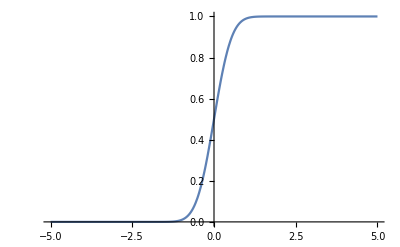

```mathematica
Plot[1/2 (1+Erf[(2 y √Log[2])/w])/.w->1,{y,-5,5}]
```

```mathematica
Convolve[1/((2x/d)^2+1),1/x,x,y,Assumptions->d>0]
```

(2 d π y)/(d^2+4 y^2)